```mathematica
Quit[];
```

```mathematica
M0=1-0.15ⅈ;
```

```mathematica
Propagator[s_,μ_,F0_,F1_,FPrime1_]:=Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](F0[s]-F1[μ^2]));
SpectralExact[s_,μ_,F0_,F1_,F2_,FPrime1_]:=ⅈ/(2π)(Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](F0[s]-F1[μ^2]))-Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](F2[s]-F1[μ^2])));
```

```mathematica
FermionF0[s_]:=s/18 (5+3Log[-1/s]);
FermionFPrime0[s_]:=1/9+1/6 Log[-1/s];
FermionF1[s_]:=s/18 (5+3Log[-1/s]+6π×ⅈ);
FermionFPrime1[s_]:=1/9+1/6 Log[-1/s]+1/3 π×ⅈ;
FermionF2[s_]:=s/18 (5+3Log[-1/s]-6π×ⅈ);
FermionP[s_,μ_]:=Propagator[s,μ,FermionF0,FermionF1,FermionFPrime1];
```

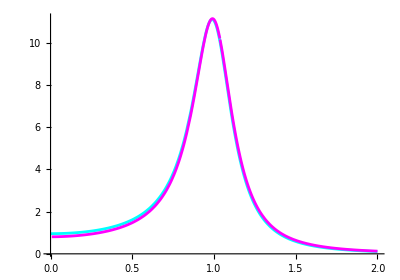

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[FermionP[s,M0]]^2},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

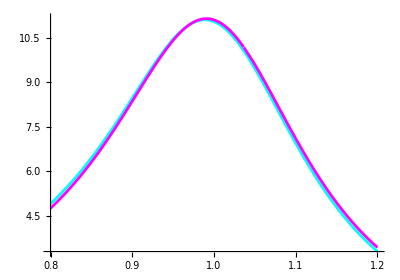

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0.64,1.44},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[FermionP[s,M0]]^2},{s,0.64,1.44},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
SpectralNWA[s_,μ_]:=-1/π Im[1/(s-μ^2)];
FermionSpectralExact[s_,μ_]:=SpectralExact[s,μ,FermionF0,FermionF1,FermionF2,FermionFPrime1];
```

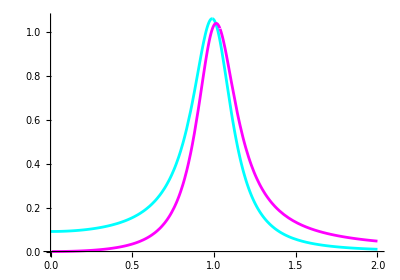

```mathematica
Show[ParametricPlot[{Sqrt[s],SpectralNWA[s,M0]},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],FermionSpectralExact[s,M0]},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
ScalarF0[s_]:=2+Log[-1/s];
ScalarFPrime0[s_]:=-1/s;
ScalarF1[s_]:=2+Log[-1/s]+2π×ⅈ;
ScalarFPrime1[s_]:=-1/s;
ScalarF2[s_]:=2+Log[-1/s]-2π×ⅈ;
ScalarP[s_,μ_]:=Propagator[s,μ,ScalarF0,ScalarF1,ScalarFPrime1];
```

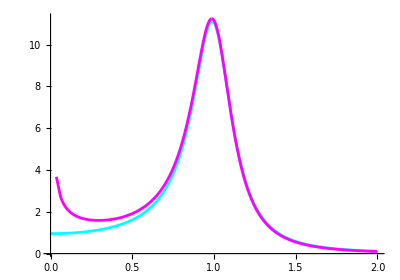

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[ScalarP[s,M0]]^2},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

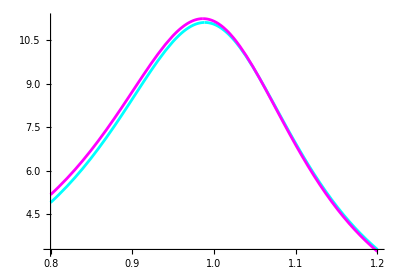

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0.64,1.44},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[ScalarP[s,M0]]^2},{s,0.64,1.44},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
ScalarSpectralExact[s_,μ_]:=SpectralExact[s,μ,ScalarF0,ScalarF1,ScalarF2,ScalarFPrime1];
```

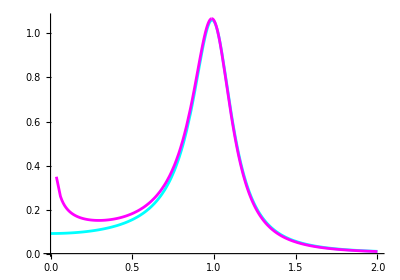

```mathematica
Show[ParametricPlot[{Sqrt[s],SpectralNWA[s,M0]},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],ScalarSpectralExact[s,M0]},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

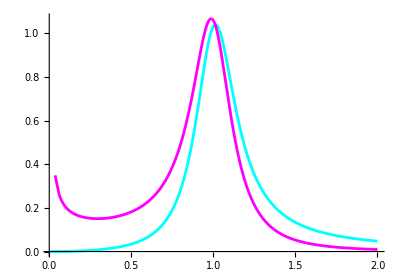

```mathematica
Show[ParametricPlot[{Sqrt[s],FermionSpectralExact[s,M0]},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],ScalarSpectralExact[s,M0]},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

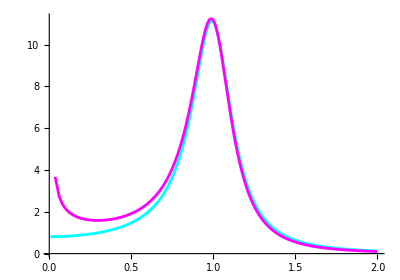

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[FermionP[s,M0]]^2},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[ScalarP[s,M0]]^2},{s,0,4},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

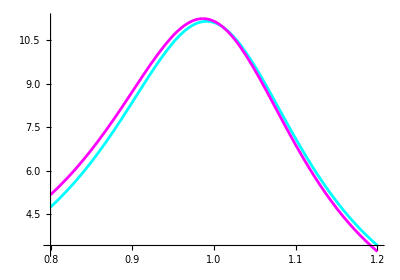

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[FermionP[s,M0]]^2},{s,0.64,1.44},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[ScalarP[s,M0]]^2},{s,0.64,1.44},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
PropagatorBranch[s_,μ_,F0s_,F1s_,FPrime1s_,Rs_]:=Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](F0s[[k]][s]-F1s[[k]][μ^2]));
SpectralExact[s_,μ_,F0s_,F1s_,F2s_,FPrime1s_,Rs_]:=ⅈ/(2π)(Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](F0s[[k]][s]-F1s[[k]][μ^2]))-Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](F2s[[k]][s]-F1s[[k]][μ^2])));
```

```mathematica
FSMixP[s_,μ_,Rs_]:=PropagatorBranch[s,μ,{FermionF0,ScalarF0},{FermionF1,ScalarF1},{FermionFPrime1,ScalarFPrime1},Rs];
FSMixSpectral[s_,μ_,Rs_]:=SpectralExact[s,μ,{FermionF0,ScalarF0},{FermionF1,ScalarF1},{FermionF2,ScalarF2},{FermionFPrime1,ScalarFPrime1},Rs];
```

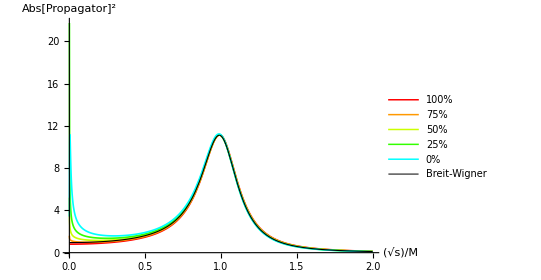

```mathematica
ParametricPlot[{{Sqrt[s],Abs[FSMixP[s,M0,{1,0}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.75,0.25}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.5,0.5}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.25,0.75}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0,1}]]^2},{Sqrt[s],Abs[s-M0^2]^-2}},{s,0,4},PlotRange->Full,AspectRatio->0.7,PlotStyle->{Directive[Hue[1],Thickness[0.003]],Directive[Hue[1.1],Thickness[0.003]],Directive[Hue[1.2],Thickness[0.003]],Directive[Hue[1.3],Thickness[0.003]],Directive[Hue[1.5],Thickness[0.003]],Directive[Black,Thickness[0.002]]},PlotLegends->{"100%","75%","50%", "25%", "0%","Breit-Wigner"},AxesLabel->{Sqrt[s]/M,Abs[Propagator]^2},MaxRecursion->15]
```

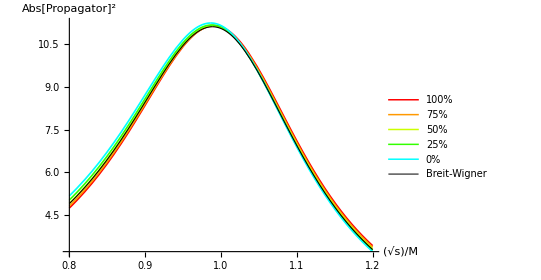

```mathematica
ParametricPlot[{{Sqrt[s],Abs[FSMixP[s,M0,{1,0}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.75,0.25}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.5,0.5}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0.25,0.75}]]^2},{Sqrt[s],Abs[FSMixP[s,M0,{0,1}]]^2},{Sqrt[s],Abs[s-M0^2]^-2}},{s,0.64,1.44},PlotRange->Full,AspectRatio->0.7,PlotStyle->{Directive[Hue[1],Thickness[0.003]],Directive[Hue[1.1],Thickness[0.003]],Directive[Hue[1.2],Thickness[0.003]],Directive[Hue[1.3],Thickness[0.003]],Directive[Hue[1.5],Thickness[0.003]],Directive[Black,Thickness[0.002]]},PlotLegends->{"100%","75%","50%", "25%", "0%","Breit-Wigner"},AxesLabel->{Sqrt[s]/M,Abs[Propagator]^2},MaxRecursion->15]
```

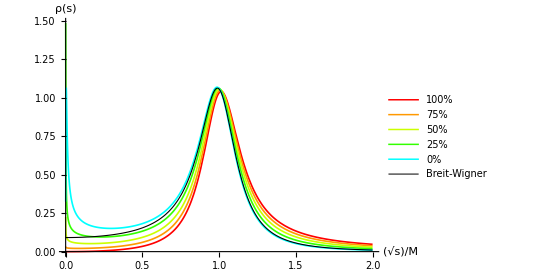

```mathematica
ParametricPlot[{{Sqrt[s],FSMixSpectral[s,M0,{1,0}]},{Sqrt[s],FSMixSpectral[s,M0,{0.75,0.25}]},{Sqrt[s],FSMixSpectral[s,M0,{0.5,0.5}]},{Sqrt[s],FSMixSpectral[s,M0,{0.25,0.75}]},{Sqrt[s],FSMixSpectral[s,M0,{0,1}]},{Sqrt[s],SpectralNWA[s,M0]}},{s,0,4},PlotRange->Full,AspectRatio->0.7,PlotStyle->{Directive[Hue[1],Thickness[0.003]],Directive[Hue[1.1],Thickness[0.003]],Directive[Hue[1.2],Thickness[0.003]],Directive[Hue[1.3],Thickness[0.003]],Directive[Hue[1.5],Thickness[0.003]],Directive[Black,Thickness[0.002]]},PlotLegends->{"100%","75%","50%", "25%", "0%","Breit-Wigner"},AxesLabel->{Sqrt[s]/M,ρ[s]},MaxRecursion->15]
```

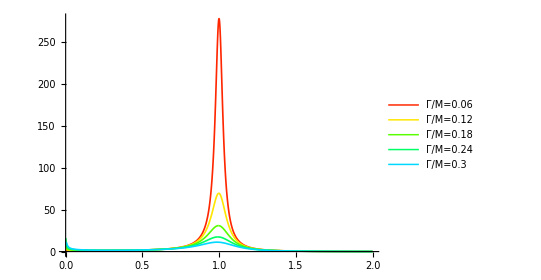

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[ScalarP[s,1-0.03ⅈ×n]]^2},{n,1,5}]],{s,0,4},PlotStyle->Table[Directive[Hue[0.9+0.125n],Thickness[0.003]],{n,1,5}],PlotLegends->Table[StringForm["Γ/M=``",0.06n],{n,1,5}],PlotRange->Full,AspectRatio->0.7,MaxRecursion->15]
```

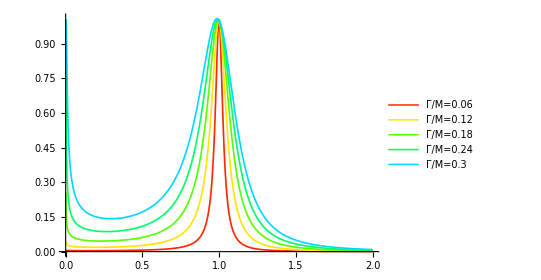

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[ScalarP[s,1-0.03ⅈ×n]]^2 Abs[ScalarP[1,1-0.03ⅈ×n]]^-2},{n,1,5}]],{s,0,4},PlotStyle->Table[Directive[Hue[0.9+0.125n],Thickness[0.003]],{n,1,5}],PlotLegends->Table[StringForm["Γ/M=``",0.06n],{n,1,5}],PlotRange->Full,AspectRatio->0.7,MaxRecursion->15]
```

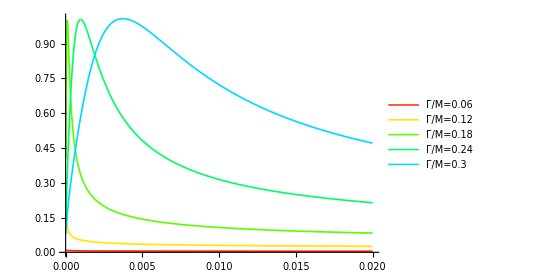

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[ScalarP[s,1-0.03ⅈ×n]]^2 Abs[ScalarP[1,1-0.03ⅈ×n]]^-2},{n,1,5}]],{s,0,0.0004},PlotStyle->Table[Directive[Hue[0.9+0.125n],Thickness[0.003]],{n,1,5}],PlotLegends->Table[StringForm["Γ/M=``",0.06n],{n,1,5}],PlotRange->Full,AspectRatio->0.7,MaxRecursion->15]
```

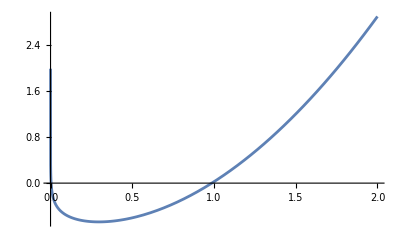

```mathematica
Plot[Re[-M^2+p^2-(Im[M^2] (-2 ⅈ π-Log[-1/M^2]+Log[-1/p^2]))/(2 π+Im[Log[-1/M^2]])]/.M->1-0.15ⅈ,{p,0,2}]
```

```mathematica
ScalarDenom=Im[ScalarF1[(1-ⅈ×Γ)^2]](s-(1-ⅈ×Γ)^2)-Im[(1-ⅈ×Γ)^2](ScalarF0[s]-ScalarF1[(1-ⅈ×Γ)^2])//ComplexExpand//Refine[#,Assumptions->{s>0,Γ>0}]&
```

-2 π+2 π s+2 ⅈ π Γ+2 π Γ^2-Arg[-1/(1-ⅈ Γ)^2]+s Arg[-1/(1-ⅈ Γ)^2]+Γ^2 Arg[-1/(1-ⅈ Γ)^2]-2 Γ Log[s]+2 Γ Log[1+Γ^2]

```mathematica
FermionDenom=Im[FermionF1[(1-ⅈ×Γ)^2]](s-(1-ⅈ×Γ)^2)-Im[(1-ⅈ×Γ)^2](FermionF0[s]-FermionF1[(1-ⅈ×Γ)^2])//ComplexExpand//Refine[#,Assumptions->{s>0,Γ>0}]&
```

-π/3+(π s)/3+1/3 ⅈ π s Γ-(2 π Γ^2)/3-1/3 π s Γ^2-(π Γ^4)/3-1/6 Arg[-1/(1-ⅈ Γ)^2]+1/6 s Arg[-1/(1-ⅈ Γ)^2]-1/3 Γ^2 Arg[-1/(1-ⅈ Γ)^2]-1/6 s Γ^2 Arg[-1/(1-ⅈ Γ)^2]-1/6 Γ^4 Arg[-1/(1-ⅈ Γ)^2]-1/3 s Γ Log[s]+1/3 s Γ Log[1+Γ^2]

```mathematica
ScalarDenomRe=-2 π+2 π s+2 π Γ^2-(2ArcTan[Γ]-π)+s (2ArcTan[Γ]-π)+Γ^2 (2ArcTan[Γ]-π)-2 Γ Log[s]+2 Γ Log[1+Γ^2]//Expand
```

-π+π s+π Γ^2-2 ArcTan[Γ]+2 s ArcTan[Γ]+2 Γ^2 ArcTan[Γ]-2 Γ Log[s]+2 Γ Log[1+Γ^2]

```mathematica
ScalarSecondPeak[A_?NumericQ]:=NSolve[ScalarDenomRe/.Γ->A, s, Reals]
```

```mathematica
Plot[ScalarSecondPeak[Γ],{Γ,0,0.15}]
```

$Aborted

```mathematica
ScalarSecondPeak[0.15]
```

{{s→0.0000138918},{s→0.973189}}